```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## u u → t t (1-loop)

generic model {Lorentz} initialized

classes model {../../Models/SMS-stop-FA/SMS-stop-FA} initialized

in total: 1 Particles insertion

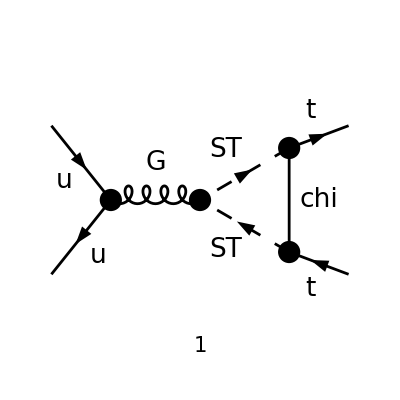

```mathematica
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { F[7],-F[7]} -> {F[9],-F[9]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],S[1],S[2],S[3],V[2],V[3],F[7],F[6],F[5],F[8],F[9]}];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{1,1},ImageSize->{ 300,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings];
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]/.{GS.GS->GS^2}]
```

in total: 1 Particles amplitude

(GS^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (-(φ(-k2)).(γ·p1).(φ(k1))+(φ(-k2)).(γ·p2).(φ(k1))-2 (φ(-k2)).(γ·q).(φ(k1))) (φ(p1,MT)).(γ·q).(γ̄)^6.(φ(-p2,MT)))/((p1+p2)^2 (q^2-mChi^2).((p1+q)^2-mST^2).((p2-q)^2-mST^2))

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify)/.{LorentzIndex[a_,D]->LorentzIndex[μ,D]}
```

-1/(p1+p2)^2 ⅈ π^2 GS.GS yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (2 (φ(-k2)).γ^μ.(φ(k1)) C_00(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+C_1(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))+2 C_11(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2) (φ(-k2)).(γ·p1).(φ(k1)) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))-2 C_12(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2) ((φ(-k2)).(γ·p2).(φ(k1)) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))+(φ(-k2)).(γ·p1).(φ(k1)) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT)))-C_2(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT))+2 C_22(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2) (φ(-k2)).(γ·p2).(φ(k1)) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT)))

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
ScalarProduct[p1,p1]=MT^2;
ScalarProduct[p2,p2]=MT^2;
ScalarProduct[p1,p2]=s/2-MT^2;
```

```mathematica
ampE = Expand[Collect[Simplify[(  ampC)/.aS->GS^2/(4 Pi),Assumptions->{GS>0}],{Pair[LorentzIndex[μ,D],Momentum[p1,D]],Pair[LorentzIndex[μ,D],Momentum[p2,D]],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[7]},FullSimplify]];
```

```mathematica
ampEsimp=FullSimplify[ampE//.{PaVe[0,0,a_,b_,c_,d_]->C00,PaVe[1,1,a_,b_,c_,d_]->C11,PaVe[1,2,a_,b_,c_,d_]->C12,PaVe[1,a_,b_,c_,d_]->C1}]
```

-1/(p1+p2)^2 ⅈ π^2 GS.GS yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (2 C00 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT)) ((C1+2 C11) (φ(-k2)).(γ·p1).(φ(k1))-(C1+2 C12) (φ(-k2)).(γ·p2).(φ(k1)))+(φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT)) ((C1+2 C11) (φ(-k2)).(γ·p2).(φ(k1))-(C1+2 C12) (φ(-k2)).(γ·p1).(φ(k1))))

```mathematica
sps=Cases2[ampEsimp,Spinor]
moms=Cases2[ampEsimp,DiracGamma]
```

{φ(k1),φ(-k2),φ(p1,MT),φ(-p2,MT)}

{(γ̄)^6,γ^μ,γ·p1,γ·p2}

```mathematica
Collect[ampEsimp,{sps[[2]].moms[[2]].sps[[1]],sps[[2]].moms[[3]].sps[[1]],sps[[2]].moms[[4]].sps[[1]]},Simplify]
```

-(2 ⅈ π^2 C00 GS.GS yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)))/(p1+p2)^2-(ⅈ π^2 GS.GS yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).(γ·p2).(φ(k1)) ((C1+2 C11) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT))-(C1+2 C12) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))))/(p1+p2)^2-(ⅈ π^2 GS.GS yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).(γ·p1).(φ(k1)) ((C1+2 C11) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))-(C1+2 C12) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT))))/(p1+p2)^2

### EFT Values (High Mass Limit)

```mathematica
C00eft=Collect[FullSimplify[Expand[(PaXEvaluate[PaVe[0,0,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/.{EulerGamma->0,ScaleMu->ScaleMu/(√(4 Pi))})]/.{s MT^2->0}],{Epsilon,s,Log[ScaleMu^2/mST^2],MT},FullSimplify];
Print["C_00 = ",C00eft];Print["-----------"];
C1eft=Collect[PaXEvaluate[PaVe[1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,0},{s,0,0}}]/.{EulerGamma->0,ScaleMu->ScaleMu/(√(4 Pi))},{Epsilon,s},FullSimplify];
Print["C_1 = ",C1eft];Print["-----------"];
C11eft=Collect[PaXEvaluate[PaVe[1,1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,0},{s,0,0}}]/.{EulerGamma->0,ScaleMu->ScaleMu/(√(4 Pi))},{Epsilon,s},FullSimplify];
Print["C_11 = ",C11eft];Print["-----------"];
C12eft=Collect[PaXEvaluate[PaVe[1,2,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,0},{s,0,0}}]/.{EulerGamma->0,ScaleMu->ScaleMu/(√(4 Pi))},{Epsilon,s},FullSimplify];
Print["C_12 = ",C12eft]
```

C_00 = ((2 mChi^6+3 mST^2 mChi^4-6 mST^2 log(mChi^2/mST^2) mChi^4-6 mST^4 mChi^2+mST^6) MT^2)/(192 (mChi^2-mST^2)^4 π^4)+(-2 log(mChi^2/mST^2) mChi^4+3 mChi^4-4 mST^2 mChi^2+mST^4)/(128 (mChi^2-mST^2)^2 π^4)+(s (6 log(mChi^2/mST^2) mChi^6-11 mChi^6+18 mST^2 mChi^4-9 mST^4 mChi^2+2 mST^6))/(1152 (mChi^2-mST^2)^4 π^4)+(log(μ^2/mST^2))/(64 π^4)+1/(64 ε π^4)

-----------

C_1 = -(-2 log(mChi^2/mST^2) mChi^4+3 mChi^4-4 mST^2 mChi^2+mST^4)/(64 (mChi^2-mST^2)^3 π^4)

-----------

C_11 = (-6 log(mChi^2/mST^2) mChi^6+11 mChi^6-18 mST^2 mChi^4+9 mST^4 mChi^2-2 mST^6)/(288 (mChi^2-mST^2)^4 π^4)

-----------

C_12 = (-6 log(mChi^2/mST^2) mChi^6+11 mChi^6-18 mST^2 mChi^4+9 mST^4 mChi^2-2 mST^6)/(576 (mChi^2-mST^2)^4 π^4)

```mathematica
A0=Collect[FullSimplify[1/2 Pi^2(C1eft+C11eft+C12eft),Assumptions->{mChi>0,mST>0}],{Epsilon,s},FullSimplify]
```

(3 mChi^4 mST^2-6 mChi^2 mST^4-12 mChi^4 mST^2 log(mChi/mST)+2 mChi^6+mST^6)/(384 π^2 (mChi^2-mST^2)^4)

```mathematica
B0=SeriesCoefficient[-2/3 C00eft,{s,0,1}]
```

-(18 mChi^4 mST^2-9 mChi^2 mST^4+6 mChi^6 log(mChi^2/mST^2)-11 mChi^6+2 mST^6)/(1728 π^4 (mChi^2-mST^2)^4)